First let’s see what the long-time stable point is for a given constant drive. Set up the differential equations, with relaxation rate gamma1 and overall decoherence rate gamma2, detuning Delta, and constant drive hy. Solve for the stable point.

```mathematica
vxdot=-γ2* vx - Δ * vy + 2*hy*vz; (*Eq 7a-c*)
vydot = -γ2*vy+Δ*vx; 
vzdot = -γ1(vz-1)-2*hy*vx;
Solve[{vxdot==0,vydot==0,vzdot==0},{vx,vy,vz}]
```

```mathematica
{{vx->(2 hy γ1 γ2)/(4 hy^2 γ2+γ1 γ2^2+γ1 Δ^2),vy->(2 hy γ1 Δ)/(4 hy^2 γ2+γ1 γ2^2+γ1 Δ^2),vz->-(-γ1 γ2^2-γ1 Δ^2)/(4 hy^2 γ2+γ1 γ2^2+γ1 Δ^2)}} (*Eq 11a-c*)
```

First, solve for the stabilization drive hy we would use with no detuning (Delta=0). Let’s solve for what the long-time stable values of vx and vz are in terms of that drive.

```mathematica
vxdotSteady = vxdot/.Δ->0;
vydotSteady = vydot/.Δ->0;
vzdotSteady = vzdot/.Δ->0;
```

```mathematica
Steady = Solve[{vxdotSteady==0,vydotSteady==0,vzdotSteady==0},{vx,vy,vz}][[1]]
```

{vx→(2 hy γ1)/(4 hy^2+γ1 γ2),vy→0,vz→(γ1 γ2)/(4 hy^2+γ1 γ2)}

```mathematica
vxSteady= vx/.Steady;
vySteady = vy/.Steady;
vzSteady = vz/.Steady;
```

Now let' s find the optimal drive hy so that we get the maximum stabilized value of vx

```mathematica
hyOpt =hy/.Solve[D[vxSteady,hy]==0,hy][[2]][[1]]
```

(√γ1 √γ2)/2

Plug in to find these max steady state values:

```mathematica
vxSteady/.hy->hyOpt
vySteady/.hy->hyOpt
vzSteady/.hy->hyOpt
```

(√γ1)/(2 √γ2)

0

1/2

Makes sense, in the γ1 = 2*γ2 limit this has a purity 3/4, and the more dephasing there is the less purity there is. Now let’s see what happens if we add back in the detuning, but use the hy we just solved for.

```mathematica
SteadyDetuned = Simplify[Solve[{vxdot==0,vydot==0,vzdot==0},{vx,vy,vz}][[1]]/.hy->hyOpt] (*Eq 12*)
```

{vx→(√γ1 γ2^(3/2))/(2 γ2^2+Δ^2),vy→(√γ1 √γ2 Δ)/(2 γ2^2+Δ^2),vz→(γ2^2+Δ^2)/(2 γ2^2+Δ^2)}

Again this seems right, as detuning grows vx shrinks and vy grows until the detuning starts to get so large that it’s hard to stabilize. Let’s look at how these values change with detuning, and also what Ramsey would give for vy. First solve for the max from Ramsey; I just did it on pencil and paper separately because Mathematica puts it in an ugly format.

```mathematica
vxSteadyD[γ1_,γ2_,Δ_]= vx/.SteadyDetuned;
vySteadyD[γ1_,γ2_,Δ_]= vy/.SteadyDetuned;
vzSteadyD[γ1_,γ2_,Δ_]= vz/.SteadyDetuned;
vyRamsey[γ2_,Δ_]=Sin[ArcTan[Δ/γ2]]E^-(γ2*ArcTan[Δ/γ2]/Δ);
```

What' s the ratio between them?

```mathematica
FullSimplify[vySteadyD[γ1,γ2,Δ]/vyRamsey[γ2,Δ]]
```

(ⅇ^((γ2 ArcTan[Δ/γ2])/Δ) √γ1 γ2^(3/2) √(1+Δ^2/γ2^2))/(2 γ2^2+Δ^2)

In the limit of small Δ:

```mathematica
Normal[Series[vySteadyD[γ1,γ2,Δ]/vyRamsey[γ2,Δ],{Δ,0,1}]] (*Eq 14*)
```

(ⅇ √γ1)/(2 √γ2)

So we have a nice expression for the improvement! In the limit of no dephasing (T2 = 2*T1) and small detuning, it’s e/Sqrt[2] = 1.922. Not bad! And unlike Ramsey, you don’t need to know a particular free evolution time to measure, this is just the long-time stabilization. Although the time for max Ramsey doesn’t depend too strongly on Δ (at least for small Δ), it’s basically just T2:

We can probably do somewhat better by using a state that DOES break down, since there can be states with long breakdown times that start from larger x values (and so have more coherence to rotate into y). Is there a way to compute this maximum vy? We know that d/dt (vy) = 0 still holds!

```mathematica
vydot==0
```

-vy γ2+vx Δ==0

Lets assume we have some breakdown time. At breakdown, vz = 0. But vx shouldn’t be constant, because it’s both decaying and rotating.

```mathematica
vxdot/.vz->0
```

-vx γ2-vy Δ

However, in the limit of small detuning, the growth of vy only affects vx to second order. So if we say vx is approximately constant up until the breakdown, then vx ~= vx(0). So we can solve vy explicitly up to the breakdown time:

```mathematica
Clear[vx0]
vybreak[t_]=vy[t]/.Simplify[DSolve[{vy'[t]==Δ*vx0-γ2*vy[t],vy[0]==0},vy[t],t]][[1]]
```

((1-ⅇ^(-t γ2)) vx0 Δ)/γ2

And vymax is just vx * Δ/γ2, but only in the limit of long breakdown. The issue is maybe vy doesn’t have a chance to GET to its maximum value before breakdown--indeed, it approaches it exponentially. Now, vy will still grow a bit after breakdown, which is also solvable because now it’s just Ramsey free decay:

```mathematica
Clear[tb];
FullSimplify[DSolve[{vy'[t]==Δ*vx[t]-γ2*vy[t],vy[0]==vybreak[tb],vx[0]==vx0,vx'[t]==-γ2*vx[t]-Δ*vy[t]},{vx[t],vy[t]},t]]
```

{{vx[t]→(ⅇ^(-((t+tb) γ2)) vx0 (ⅇ^(tb γ2) γ2 Cos[t Δ]-(-1+ⅇ^(tb γ2)) Δ Sin[t Δ]))/γ2,vy[t]→(ⅇ^(-((t+tb) γ2)) vx0 ((-1+ⅇ^(tb γ2)) Δ Cos[t Δ]+ⅇ^(tb γ2) γ2 Sin[t Δ]))/γ2}}

Note that here we’re starting t=0 at the breakdown time. So if we can find an expression for the breakdown time in terms of vx[0], then we have a full analytic solution for the best way to maximize vy (in the limit of small detuning). Since we have small detuning, let’s see if the series expansion is simpler:

```mathematica
Normal[Series[(ⅇ^(-((t+tb) γ2)) vx0 ((-1+ⅇ^(tb γ2)) Δ Cos[t Δ]+ⅇ^(tb γ2) γ2 Sin[t Δ]))/γ2,{Δ,0,1}]]
```

(ⅇ^(-((t+tb) γ2)) vx0 (-1+ⅇ^(tb γ2)+ⅇ^(tb γ2) t γ2) Δ)/γ2

That' s not too bad. I bet we can maximize that!

```mathematica
FullSimplify[Solve[D[(ⅇ^(-((t+tb) γ2)) vx0 (-1+ⅇ^(tb γ2)+ⅇ^(tb γ2) t γ2) Δ)/γ2,t]==0],Assumptions->tb>0&&γ2>0] (*Output is Eq 21*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→ⅇ^(-tb γ2)/γ2}}

Plug this time back in to find the maximum vy

```mathematica
Simplify[(ⅇ^(-((t+tb) γ2)) vx0 (-1+ⅇ^(tb γ2)+ⅇ^(tb γ2) t γ2) Δ)/γ2/.t->ⅇ^(-γ2 tb)/γ2] (*Output is Eq 22*)
```

(ⅇ^(-ⅇ^(-tb γ2)) vx0 Δ)/γ2

There’s an exact expression for the breakdown time, here shown when vz(0)>0, vy(0)=0, temperature = 0.

```mathematica
a[vx0_,T1_,T2_] = Sqrt[vx0^2/(T2/(4*T1))-1]; (*Eq 24 and 25*)
vz0[vx0_]=Sqrt[1-vx0^2];
tb[vx0_,T1_,T2_] = T1/a[vx0,T1,T2]*(ArcTan[1/a[vx0,T1,T2]]+ArcTan[(2*vz0[vx0]-1)/a[vx0,T1,T2]])+T1/2*Log[((2*vz0[vx0]-1)^2+a[vx0,T1,T2]^2)/(1+a[vx0,T1,T2]^2)];
```

Meanwhile the best Ramsey value is, again, Δ/(γ2*e), so we can take the ratio Rv of vy (stabilized) to vy (Ramsey). We need to check whether there’s a breakdown time, and use the stable-state solution if there isn’t

```mathematica
Rv[vx0_,T1_,T2_]=If[vx0>1/2*Sqrt[T2/T1],E^(1-E^-(tb[vx0,T1,T2]/T2))*vx0,E*vx0] (*Eq 22, plus a bit of logic so that it also handles stable solutions*)
```

If[vx0>(√(T2/T1))/2,ⅇ^(1-ⅇ^(-tb[vx0,T1,T2]/T2)) vx0,ⅇ vx0]

And  now we can maximize over vx0 quite easily!

```mathematica
NMaximize[Rv[vx0,1,1],{vx0,0.7,1}][[1]]
```

1.49008

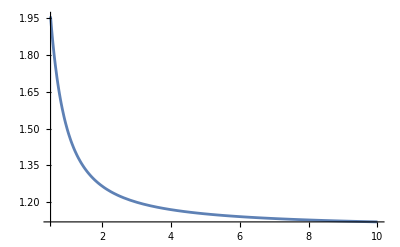

```mathematica
Plot[NMaximize[Rv[vx0,T1,1],{vx0,0.7,1}][[1]],{T1,0.5,10},PlotRange->All] (*Fig 3a bottom right*)
```

It’s useful  to have some data for export.

```mathematica
Rvmaxes = Table[{T1,NMaximize[Rv[vx0,T1,1],{vx0,0.7,1}][[1]]},{T1,0.5,5,0.01}];
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

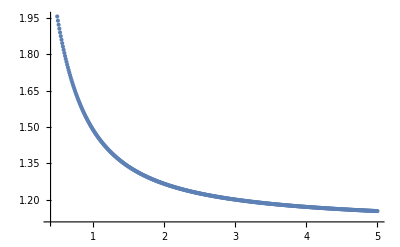

```mathematica
ListPlot[Rvmaxes,PlotRange->All]
```

```mathematica
Rvmaxes//TableForm;
```

```mathematica
Rvpairs = Table[Max[Re[hasBreak[Sin[Pi*theta],T1,1]*Rv[Sin[Pi*theta],T1,1]],(1-hasBreak[Sin[Pi*theta],T1,1])*RvNB[Sin[Pi*theta]]],{theta,0.001,0.499,0.001},{T1,0.5,10,0.1}];
```

General::munfl: Exp[-1480.51] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
Rvpairs = Table[Rv[Sin[Pi*theta],T1,1],{theta,0.005,0.495,0.005},{T1,0.5,10,0.1}];
```

```mathematica
Rvpairs//TableForm;
```

Also want the time at which the max happens as a function of initial state for our T1/T2 = 0.75

```mathematica
tmax[vx0_,T1_,T2_]=If[vx0>1/2*Sqrt[T2/T1],tb[vx0,T1,T2]+T2*E^-(tb[vx0,T1,T2]/T2),0]
```

If[vx0>(√(T2/T1))/2,tb[vx0,T1,T2]+T2 ⅇ^(-tb[vx0,T1,T2]/T2),0]

```mathematica
tmaxpairs = Table[{theta,tmax[Sin[Pi*theta],0.75,1]},{theta,0.01,0.49,0.5/32}];
```

```mathematica
tmaxpairs//TableForm
```

0.01 | 0
0.025625 | 0
0.04125 | 0
0.056875 | 0
0.0725 | 0
0.088125 | 0
0.10375 | 0
0.119375 | 0
0.135 | 0
0.150625 | 0
0.16625 | 0
0.181875 | 0
0.1975 | 17.5558
0.213125 | 3.79793
0.22875 | 2.27927
0.244375 | 1.68201
0.26 | 1.38777
0.275625 | 1.2276
0.29125 | 1.13553
0.306875 | 1.08094
0.3225 | 1.04802
0.338125 | 1.02807
0.35375 | 1.01602
0.369375 | 1.00883
0.385 | 1.00464
0.400625 | 1.00228
0.41625 | 1.00102
0.431875 | 1.0004
0.4475 | 1.00013
0.463125 | 1.00003
0.47875 | 1.

```mathematica
Rvmaxes = Table[{T1,NMaximize[Rv[vx0,T1,1],{vx0,0.7,1}][[1]]},{T1,0.5,5,0.01}];
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
theta/.NMaximize[Rv[Sin[Pi*theta],1,1],{theta,1/2,1}][[2]]
```

0.805464

```mathematica
thetamaxes = Table[{T1,theta/.NMaximize[Rv[Sin[Pi*theta],T1,1],{theta,ArcSin[1/2/Sqrt[T1]]/Pi,0.5}][[2]]},{T1,0.5,5,0.01}];
```

```mathematica
thetamaxes//TableForm;
```

```mathematica
tmaxes = Table[{tmax[Sin[Pi*thetamaxes[[ii,2]]],thetamaxes[[ii,1]],1]},{ii,1,451}];
tmaxes//TableForm;
```

```mathematica
thetamaxes[[450,1]]
```

4.99

```mathematica
tmaxtheta = Table[{theta,tmax[Sin[Pi*theta],0.75,1]},{theta,0.01,0.49,0.48/32}];
```

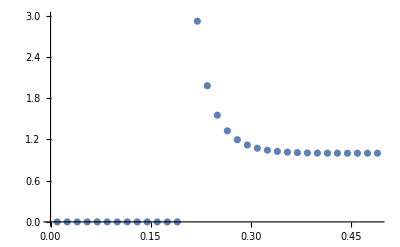

```mathematica
ListPlot[tmaxtheta]
```